```mathematica
(*SuperradiantLaser, cumulant;
  using bash;
  Variables v.s. repumping w*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*Parameters*)
nMax=100;
init=.1;
interval=.1;
nAtomAve = 100;
(*Get data*)
(*Set up bins*)
nAtom = Table[0,{i,nMax}];
intensity=Table[0,{i,nMax}];
szFinal=Table[0,{i,nMax}];
inversionAve =Table[0,{i,nMax}];
tau=Table[0,{i,nMax}];
(*Input values*)
For[i=0,i<nMax,i++,
tau[[i+1]] =init+interval i;
tauForm= NumberForm[tau[[i+1]],{10,1}];
nAtomData=Flatten[Import[NotebookDirectory[]<>"pois_tau0"<>ToString[tauForm]<>"_g2_k40_N100/nAtom.dat"]];
intensityData=Flatten[Import[NotebookDirectory[]<>"pois_tau0"<>ToString[tauForm]<>"_g2_k40_N100/intensity.dat"]];
szFinalData=Flatten[Import[NotebookDirectory[]<>"pois_tau0"<>ToString[tauForm]<>"_g2_k40_N100/szFinal.dat"]];
inversionAveData=Flatten[Import[NotebookDirectory[]<>"pois_tau0"<>ToString[tauForm]<>"_g2_k40_N100/inversionAve.dat"]];
(*x=Cases[x,Except[0|0.]];*)
nAtom[[i+1]]=Last[nAtomData];
intensity[[i+1]]=Last[intensityData];
szFinal[[i+1]]=Last[szFinalData];
inversionAve[[i+1]]=Last[inversionAveData];
]
```

```mathematica
(*Combine data*)
nAtomPlot=Transpose@{ tau,nAtom};
intensityPlot=Transpose@{ tau,intensity};
szFinalPlot=Transpose@{tau,szFinal};
inversionAvePlot=Transpose@{tau,inversionAve};
```

```mathematica
(*Plot*)
```

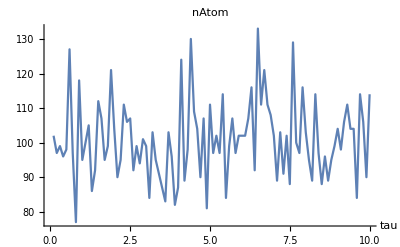

```mathematica
ListLinePlot[nAtomPlot,PlotRange->All,PlotLabel->"nAtom",AxesLabel->{"tau"}]
```

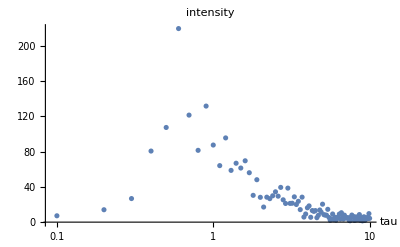

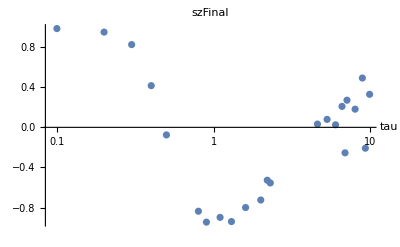

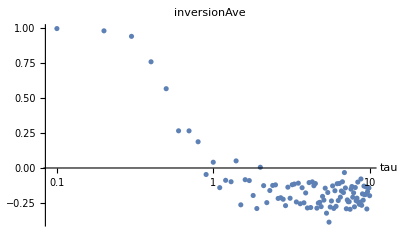

```mathematica
ListLogLinearPlot[intensityPlot,PlotRange->All,PlotLabel->"intensity",AxesLabel->{"tau"}]
ListLogLinearPlot[szFinalPlot,PlotRange->All,PlotLabel->"szFinal",AxesLabel->{"tau"}]
ListLogLinearPlot[inversionAvePlot,PlotRange->All,PlotLabel->"inversionAve",AxesLabel->{"tau"}]
```